# NLO Evolution of Transversity Distributions

## Defining constants, special functions, and QCD splitting functions

```mathematica
(* Settings that the user can change*)
Subscript[Λ, QCD]:=0.231 (* QCD scale parameter in GeV *)
Subscript[N, f]=4; (* Number of quark flavors *)
Q0sq=4.0;(* initial scale in GeV^2, at which an initial PDF is provided by the user *)
Qsq=200.0;(* final scale of the evolution in GeV^2. Q^2>Subscript[Q, 0]^2 for forward evolution or Q^2<Subscript[Q, 0]^2 for backward evolution *)
sign=-1;(* The parameter η in the splitting functions. η=+1: Subscript[xΔ, T] Subscript[q, i]+Subscript[xΔ, T] Subscript[q̄, i] type distribution; η=-1: Subscript[xΔ, T] Subscript[q, i]-Subscript[xΔ, T] Subscript[q̄, i] type distribution *)
nt=100;(* number of t steps used in the x-space evolution. The number of x steps is by default same with the number of x points in the user-supplied PDF. The moment method does not discretize the t-space. *)
order=2;(* 1 for leading order, 2 for next-to-leading order evolution *)
analy=False; (* boolean variable. True for an analytic approximation of the strong coupling constant Subscript[α, S], False for a numerical solution of the evolution equation for Subscript[α, S] *)

(* Theory constants *)
Subscript[N, C]=3;
Subscript[C, G]=Subscript[N, C];
Subscript[C, F]=(Subscript[N, C]^2-1)/(2 Subscript[N, C]);
Subscript[T, R]=1/2;
Subscript[T, f]=Subscript[T, R] Subscript[N, f];
Subscript[β, 0]=11/3 Subscript[C, G]-4/3 Subscript[T, R] Subscript[N, f];
(*Subscript[β, 1]=0 for LO, Subscript[β, 1] for NLO evolution*)
Subscript[β, 1]=If[order==1,0,34/3 Subscript[C, G]^2-10/3 Subscript[C, G] Subscript[N, f]-2 Subscript[C, F] Subscript[N, f]];

(* Special functions *)
ψ[z_]:=PolyGamma[0, z]
ψp[z_]:=PolyGamma[1, z]
ψpp[z_]:=PolyGamma[2, z]
Subscript[S, 1][n_]:=EulerGamma+ψ[n+1];
Subscript[S, 2][n_]:=Zeta[2]-ψp[n+1];
Subscript[S, 3][n_]:=Zeta[3]+1/2 ψpp[n+1];
Subscript[S, p,k_][n_,η_]:=1/2(1+η)Subscript[S, k][n/2]+1/2(1-η)Subscript[S, k][(n-1)/2]
Sp[n_,η_,k_]:=2^(k-1)Sum[(1+(-1)^j)/j^k,{j,1,N}]
G[n_]:=ψ[(n+1)/2]-ψ[n/2]
S̃[n_,η_]:=-5/8 Zeta[3]+η((Subscript[S, 1][n])/n^2-Zeta[2]/2 G[n]+NIntegrate[t^(n-1)PolyLog[2,t]/(1+t),{t,0,1},PrecisionGoal->8,AccuracyGoal->8,Method->{"LocalAdaptive",Method->{"GaussKronrodRule","Points"->9}}])

(* Define the strong coupling constant Subscript[α, S]*)
Subscript[a, S,num][a0_,Qαsq_,t_]:=NDSolve[{a'[t]==-Subscript[β, 0](a[t])^2-Subscript[β, 1](a[t])^3,a[Log[Qαsq]]==a0/(4Pi)},a,{t,-1.6,10}]
(*The initial condition for the numerical Subscript[α, S] evolution is set to be Subscript[α, S]=0.118 at Q^2=Subscript[M, Z]^2=91.1876^2*)
Subscript[α, S][t_]:=If[analy,(4Pi)/(Subscript[β, 0](t-2Log[Subscript[Λ, QCD]]))-4Pi Subscript[β, 1]/Subscript[β, 0]^3 Log[t-2Log[Subscript[Λ, QCD]]]/(t-2Log[Subscript[Λ, QCD]])^2,(a/.First[Subscript[a, S,num][0.118,91.1876^2,tt]])[t]4Pi];

(* Mellin transform *)
M[f_,s_]:=∫_0^1 t^(s-1)f[t]ⅆt
Subscript[M, num][f_,s_]:=NIntegrate[t^(s-1)f[t],{t,0,1}]

(* The Mellin moments of the LO and NLO transversity splitting function *)
Subscript[MΔTP, LO][n_]:=Subscript[C, F](3/2-2 Subscript[S, 1][n])
Subscript[MΔTP, NLO][n_,η_]:=If[order==1,0,Subscript[C, F]^2(3/8+(1-η)/(n(n+1))-3 Subscript[S, 2][n]-4 Subscript[S, 1][n](Subscript[S, 2][n]-Subscript[S, p,2][n,η])-8 S̃[n,η]+Subscript[S, p,3][n,η])+1/2 Subscript[C, F] Subscript[N, C](17/12-(1-η)/(n(n+1))-134/9 Subscript[S, 1][n]+22/3 Subscript[S, 2][n]+4 Subscript[S, 1][n](2 Subscript[S, 2][n]-Subscript[S, p,2][n,η])+8 S̃[n,η]-Subscript[S, p,3][n,η])+2/3 Subscript[C, F] Subscript[T, f](-1/4+10/3 Subscript[S, 1][n]-2 Subscript[S, 2][n])]

(* Plus function regularization, for the Mellin moments as well *)
SubPlus[M][f_,g_,s_]:=NIntegrate[(t^(s-1)f[t]-f[1])g[t],{t,0,1}]
(* When there are k powers of Log[1-x], follow Eq. 29 of https://arxiv.org/pdf/hep-ph/9806280
In Eq. 29, there is a typo and the factor of x^m is missing *)
Mln[k_,f_,g_,s_]:=NIntegrate[t^(s-1)(f[t]-f[1])Log[1-t]^k g[t],{t,0,1}]

(* LO and NLO x-space transversity splitting functions *)
q[x_]:=1/(1-x)
Subscript[δTP, qq][x_]:=2x SubPlus[q][x]
Subscript[ΔTP, qq,LO][x_]:=Subscript[C, F](2x SubPlus[q][x]+3/2 DiracDelta[1-x])
Subscript[ΔTP, qq,NLO][x_]:=If[order==1,0,Subscript[C, F]^2(1-x-(3/2+2Log[1-x])Log[x]Subscript[δTP, qq][x]+(3/8-π^2/2+6Zeta[3])DiracDelta[1-x])+1/2 Subscript[C, F] Subscript[N, C](-(1-x)+(67/9+11/3 Log[x]+Log[x]^2-π^2/3)Subscript[δTP, qq][x]+(17/12+(11 π^2)/9-6Zeta[3])DiracDelta[1-x])+2/3 Subscript[C, F] Subscript[T, f]((-Log[x]-5/3)Subscript[δTP, qq][x]-(1/4+π^2/3)DiracDelta[1-x])]
S2[x_]:=-2PolyLog[2,-x]-2Log[x]Log[1+x]+1/2 Log[x]^2-π^2/6
Subscript[ΔTP, q q̄,NLO][x_]:=If[order==1,0,Subscript[C, F](Subscript[C, F]-1/2 Subscript[N, C])(-(1-x)+2S2[x](-2x)/(1+x))]
Subscript[ΔTP, qq,NLO,η_][x_]:=Subscript[ΔTP, qq,NLO][x]+η Subscript[ΔTP, q q̄,NLO][x]
```

## Checking the agreement of the analytic continuations of the Mellin moments with the x-space splitting functions

### LO transversity moments

```mathematica
(* The 1st to 10th moments of the LO splitting function. The first line of output is the Mellin transform of the x-space expression. The second line is the output of the expression of the splitting function in Mellin space. The agreement shows the correctness of the Mellin transform. *)
```

```mathematica
Table[Subscript[C, F](SubPlus[M][x↦2x,q,s]+3/2),{s,1,10}]
Table[N[Subscript[MΔTP, LO][s]],{s,1,10}]
```

{-0.666667,-2.,-2.88889,-3.55556,-4.08889,-4.53333,-4.91429,-5.24762,-5.54392,-5.81058}

{-0.666667,-2.,-2.88889,-3.55556,-4.08889,-4.53333,-4.91429,-5.24762,-5.54392,-5.81058}

### NLO transversity moments

```mathematica
plusPart[x_]=Coefficient[Coefficient[Subscript[ΔTP, qq,NLO,-1][x],SubPlus[q][x],1],Log[1-x],0];
plusPartLog[x_]=Coefficient[Coefficient[Subscript[ΔTP, qq,NLO,-1][x],SubPlus[q][x],1],Log[1-x],1];
constantTerm=Coefficient[Subscript[ΔTP, qq,NLO,-1][x],DiracDelta[1-x],1];
plusMoment[s_]:=SubPlus[M][plusPart,q,s]+Mln[1,plusPartLog,q,s]
remainingPartIntegrand[x_]=Coefficient[Coefficient[Subscript[ΔTP, qq,NLO,-1][x],SubPlus[q][x],0],DiracDelta[1-x],0];
remainingPart[s_]:=Subscript[M, num][remainingPartIntegrand,s]
PqqNLOmoment[s_]:=remainingPart[s]+plusMoment[s]+constantTerm
numerical=Table[PqqNLOmoment[s],{s,1,100}]
analytic=Table[N[Subscript[MΔTP, NLO][s,-1]],{s,1,100}]
```

{-8.12963,-11.5894,-13.9897,-15.878,-17.4499,-18.8021,-19.9912,-21.0537,-22.0149,-22.8928,-23.7011,-24.4503,-25.1485,-25.8024,-26.4173,-26.9978,-27.5475,-28.0695,-28.5666,-29.0411,-29.4949,-29.9297,-30.3472,-30.7487,-31.1354,-31.5082,-31.8683,-32.2164,-32.5534,-32.8798,-33.1964,-33.5038,-33.8024,-34.0928,-34.3754,-34.6506,-34.9188,-35.1804,-35.4356,-35.6848,-35.9282,-36.1662,-36.3989,-36.6265,-36.8494,-37.0677,-37.2815,-37.4911,-37.6967,-37.8983,-38.0961,-38.2903,-38.481,-38.6684,-38.8524,-39.0333,-39.2112,-39.3862,-39.5583,-39.7276,-39.8943,-40.0584,-40.22,-40.3792,-40.536,-40.6905,-40.8428,-40.993,-41.141,-41.2871,-41.4311,-41.5732,-41.7134,-41.8518,-41.9884,-42.1233,-42.2565,-42.388,-42.518,-42.6463,-42.7731,-42.8985,-43.0223,-43.1447,-43.2658,-43.3855,-43.5038,-43.6208,-43.7366,-43.8511,-43.9644,-44.0765,-44.1874,-44.2972,-44.4058,-44.5134,-44.6199,-44.7253,-44.8297,-44.9331}

{-8.12963,-11.5741,-13.9897,-15.8761,-17.4499,-18.8016,-19.9912,-21.0536,-22.0149,-22.8927,-23.7011,-24.4502,-25.1485,-25.8024,-26.4173,-26.9978,-27.5475,-28.0695,-28.5666,-29.0411,-29.4949,-29.9297,-30.3472,-30.7487,-31.1354,-31.5082,-31.8683,-32.2164,-32.5534,-32.8798,-33.1964,-33.5038,-33.8024,-34.0928,-34.3754,-34.6506,-34.9188,-35.1804,-35.4356,-35.6848,-35.9282,-36.1662,-36.3989,-36.6265,-36.8494,-37.0677,-37.2815,-37.4911,-37.6967,-37.8983,-38.0961,-38.2903,-38.481,-38.6684,-38.8524,-39.0333,-39.2112,-39.3862,-39.5583,-39.7276,-39.8943,-40.0584,-40.22,-40.3792,-40.536,-40.6905,-40.8428,-40.993,-41.141,-41.2871,-41.4311,-41.5732,-41.7134,-41.8518,-41.9884,-42.1233,-42.2565,-42.388,-42.518,-42.6463,-42.7731,-42.8985,-43.0223,-43.1447,-43.2658,-43.3855,-43.5038,-43.6208,-43.7366,-43.8511,-43.9644,-44.0765,-44.1874,-44.2972,-44.4058,-44.5134,-44.6199,-44.7253,-44.8297,-44.9331}

```mathematica
Max[Abs[(numerical-analytic)/analytic]]
(*The maximum difference between the numerically calculated moments of the NLO splitting functions expression in the x space, and the analytic expression in the Mellin space, in the 100 moments printed above*)
```

0.00132516

```mathematica
Abs[(numerical-analytic)/analytic]
```

{1.10126×10^-10,0.00132516,7.45973×10^-10,0.000117585,4.95837×10^-12,0.0000245305,6.06005×10^-14,7.723×10^-6,4.03445×10^-15,3.0977×10^-6,1.94865×10^-15,1.45686×10^-6,2.26031×10^-15,7.66672×10^-7,2.01726×10^-15,4.38606×10^-7,2.81915×10^-10,2.67351×10^-7,2.71871×10^-10,1.71616×10^-7,2.6333×10^-10,1.14829×10^-7,2.55946×10^-10,7.95174×10^-8,2.49479×10^-10,5.66763×10^-8,2.43753×10^-10,4.14005×10^-8,2.38635×10^-10,3.08874×10^-8,2.34023×10^-10,2.34702×10^-8,2.29837×10^-10,1.81221×10^-8,2.26016×10^-10,1.41912×10^-8,2.22507×10^-10,1.12523×10^-8,2.19271×10^-10,9.02115×10^-9,2.16273×10^-10,7.30397×10^-9,8.54218×10^-10,5.32907×10^-9,8.43767×10^-10,4.28202×10^-9,8.33974×10^-10,3.44935×10^-9,8.24771×10^-10,2.781×10^-9,8.16098×10^-10,2.23997×10^-9,8.07903×10^-10,1.79856×10^-9,8.00142×10^-10,1.43584×10^-9,7.92777×10^-10,1.1358×10^-9,7.85772×10^-10,8.86084×10^-10,7.79095×10^-10,6.77064×10^-10,7.72725×10^-10,5.01188×10^-10,7.66632×10^-10,3.52477×10^-10,7.60797×10^-10,2.26165×10^-10,2.9916×10^-9,2.10855×10^-9,2.9675×10^-9,2.61703×10^-11,7.44657×10^-10,5.31152×10^-11,7.3968×10^-10,1.2148×10^-10,7.34882×10^-10,1.80613×10^-10,7.3025×10^-10,2.37064×10^-9,2.85616×10^-9,2.39863×10^-9,7.21443×10^-10,3.15417×10^-10,7.17251×10^-10,3.49402×10^-10,2.79475×10^-9,2.45275×10^-9,2.7749×10^-9,2.46301×10^-9,2.7553×10^-9,2.4702×10^-9,2.73589×10^-9,2.47472×10^-9,2.71664×10^-9,4.66109×10^-10,6.94556×10^-10,4.81766×10^-10,6.91124×10^-10,4.95582×10^-10}

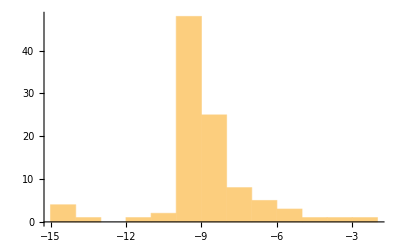

```mathematica
Histogram[Log10[Abs[(numerical-analytic)/analytic]]]
```

## NLO evolution by the Bjorken x-space DGLAP equations

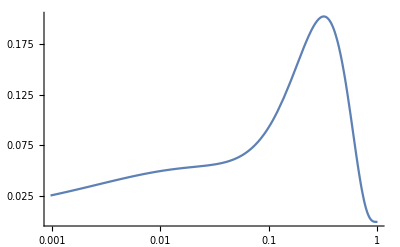

```mathematica
SetDirectory[NotebookDirectory[]];
pdfTab=Import["input_upd.dat","Table","FieldSeparators"->" ","LineSeparators"->"\n"];
pdf=Interpolation[pdfTab];
Plot[pdf[x],{x,0,1},ScalingFunctions->{"Log", "Linear"}]
(*read in initial PDF (supplied by the user). This is the initial PDF for both methods*)(* Supply initial PDF as a data file of two columns with the first column being x values and the second column being the parton distribution function values at the corresponding x, multiplied by x, i.e. x*f(x) *)
```

```mathematica
Dimensions[pdfTab]
```

{3001,2}

```mathematica
(*Due to the slowness of Mathematica compared to Python, the fineness of the x-space grid is reduced by a factor of 10 in the code below, i.e., Subscript[N, x]=300 rather than 3000. *)
```

```mathematica
Evolve[pdfTab_,Q0sq_,Qsq_,Nt_,eta_]:=Module[{z,xs,ys,ts,dts,Nx,res,splitting,intermediate1,intermediate2,integrand1,integrand2,integrand2At1,addition,integrand,integrand3,pdff,addPart,addPart2,addPart3,addPart4,integrand4,integrand5,convolution,IntegrationStep,x,alpt},{
xs=pdfTab[[;;;;10,1]];
ys=pdfTab[[;;;;10,2]];
ts=Array[# &, Nt+1, {Log[Q0sq],Log[Qsq]}];
dts=ts[[2;;Length[ts]]]-ts[[1;;Length[ts]-1]];
Nx=Length[xs];
res=ys;
splitting=Subscript[ΔTP, qq,LO][z]+alpt*(Subscript[ΔTP, qq,NLO,eta][z]);
integrand1=Coefficient[Coefficient[splitting,SubPlus[q][z],0], DiracDelta[-1+z],0];
(* The plus-regularized terms *)
integrand2=Coefficient[splitting,SubPlus[q][z],1];
integrand2At1=Limit[integrand2,z->1];
(* And the Dirac delta contributions *)
addition=pdff[x] (Coefficient[splitting,DiracDelta[-1+z],1]+integrand2At1 Log[1-x]);
intermediate1=N[FullSimplify[pdff[x/z]*integrand1+(pdff[x/z]integrand2-pdff[x]integrand2At1)*q[z]]];
integrand3[pdff_]:=Compile[{{x,_Real},{z,_Real},{alpt,_Real}},Evaluate[intermediate1],CompilationTarget->"C",RuntimeOptions->"Speed"];
intermediate2=N[FullSimplify[N[addition]]];
addPart2[pdff_]:=Compile[{{x,_Real},{alpt,_Real}},Evaluate[intermediate2],CompilationTarget->"C",RuntimeOptions->"Speed"];
convolution[x_?NumericQ,alpt_?NumericQ,pdff_]:=NIntegrate[integrand5[x,z,alpt],{z,x,1},Method->{Automatic,"SymbolicProcessing"->0},PrecisionGoal->6]+addPart4[x,alpt];
IntegrationStep[ys_,xs_,t_?NumericQ,dt_,pdf_]:=ArrayPad[ParallelTable[N[ys[[i]]+dt(Subscript[α, S][t])/(2π)convolution[xs[[i]],(Subscript[α, S][t])/(2π),pdf]],{i,2,Nx-1}],1];
Monitor[Do[{
pdff=Interpolation[Transpose[{xs,res}]];
integrand4=integrand3[pdff];
integrand5[x_?NumericQ,z_?NumericQ,alpt_?NumericQ]:=integrand4[x,z,alpt];
addPart3=addPart2[pdff];
addPart4[x_?NumericQ,alpt_?NumericQ]:=addPart3[x,alpt];
res=IntegrationStep[res,xs,ts[[i]],dts[[i]],pdff];
},{i,1,Nt}],ProgressIndicator[i,{1,Nt}]];
res
}]
res=Evolve[pdfTab,Q0sq,Qsq,nt,sign][[1]];(*give the initial PDF array, initial energy scale, final scale, number of t steps, and plus or minus type evolution to the function "Evolve", then the output is the evolved x*PDF*)
```

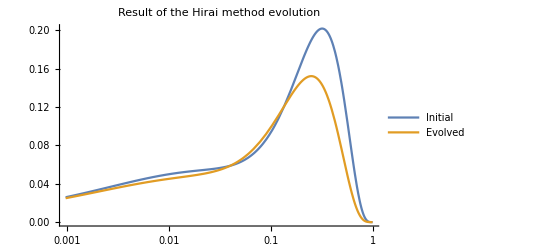

```mathematica
resInterpolation=Interpolation[Transpose[{pdfTab[[;;;;10,1]], res}]];
Plot[{pdf[x],resInterpolation[x]},{x,0,1},ScalingFunctions->{"Log", "Linear"},PlotLegends->{"Initial","Evolved"},PlotLabel->"Result of the Hirai method evolution"]
```

```mathematica
(*Export["mathematica_hirai_ana.dat",Transpose[{pdfTab[[;;;;10,1]], res}],"Table","FieldSeparators"->" "]*)
```

```mathematica
Export["mathematica_hirai_num.dat",Transpose[{pdfTab[[;;;;10,1]], res}],"Table","FieldSeparators"->" "]
```

mathematica_hirai_num.dat

## NLO evolution by the Mellin space equation

```mathematica
γ[dig_,t_]:=2/3(dig N[Log[10]]+Log[2 t])
Subscript[c, M_,k_]:=(-1)^k(Subscript[d, M]-∑_(m=0)^k (M/(M+m)Binomial[M+m,2m]N[2^(2m)]))
Subscript[d, M_]:=((3+N[√8])^M+(3-N[√8])^M)/2;
CohenInverseLaplace[fbar_,t_,M_]:=ⅇ^(γ[Round[1.5(M-1)],t]/2)/t(1/2 Re[fbar[γ[Round[1.5(M-1)],t]/(2t)]]-∑_(k=0)^(M-1) (Subscript[c, M,k]/Subscript[d, M] Re[fbar[(γ[Round[1.5(M-1)],t]+2(k+1)π ⅈ)/(2t)]]))
CohenInverseMellin[fbar_, x_, degree_]:=CohenInverseLaplace[fbar,-Log[x],degree]
```

```mathematica
MEvolve[pdfTab_,Q0sq_,Qsq_,η_,deg_]:=Module[{aQ0,aQ,xs,ys,pdf,EvolveMoment,EvolveMoment2,Nx},{
xs=pdfTab[[All,1]];
ys=pdfTab[[All,2]];
(*The initial PDF is given as x*f(x), it is divided by x in the next line to obtain f(x) itself*)
ys=ys/(xs+10^-8);
Nx=Length[xs];
ys[[1]]=0;
ys[[Nx]]=0;
pdf=Interpolation[Transpose[{xs,ys}]];
aQ0=N[Subscript[α, S][Log[Q0sq]]];
aQ=N[Subscript[α, S][Log[Qsq]]];
(* The evolution equation at NLO, according to Vogelsang 1997, i.e. Eq. 20 of https://arxiv.org/abs/hep-ph/9706511v2 *)
EvolveMoment[n_]:=(1+(aQ0-aQ)/(π Subscript[β, 0])(N[Subscript[MΔTP, NLO][n,η]]-Subscript[β, 1]/(2 Subscript[β, 0])Subscript[MΔTP, LO][n]))(aQ/aQ0)^(-2/Subscript[β, 0]Subscript[MΔTP, LO][n])NIntegrate[t^(n-1)pdf[t],{t,0,1},PrecisionGoal->8,AccuracyGoal->8,Method->{"LocalAdaptive",Method->{"GaussKronrodRule","Points"->9}}];
Interpolation[Transpose[{Join[{0},xs[[2;;Nx-1;;30]],{1}],Join[{0},ParallelTable[CohenInverseMellin[EvolveMoment,x,deg],{x,xs[[2;;Nx-1;;30]]}],{0}]}]]
}]
resM=MEvolve[pdfTab,Q0sq,Qsq,sign,11][[1]];
(*11 is the approximation degree of the inverse Laplace series*)
```

General::munfl: (-1.)^(140.675+243.469 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

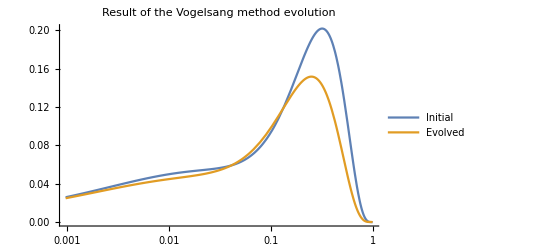

```mathematica
Plot[{pdf[x],x*resM[x]},{x,0,1},ScalingFunctions->{"Log","Linear"},PlotLegends->{"Initial","Evolved"},PlotLabel->"Result of the Vogelsang method evolution"]
```

```mathematica
xs=Join[{0},pdfTab[[2;;Length[xs]-1;;30,1]],{1}];
(*Export["mathematica_vogelsang_ana.dat",
Transpose[{xs,Table[x*resM[x],{x,xs}]}],"Table","FieldSeparators"->" "]*)
Export["mathematica_vogelsang_num.dat",
Transpose[{xs,Table[x*resM[x],{x,xs}]}],"Table","FieldSeparators"->" "]
```

mathematica_vogelsang_num.dat

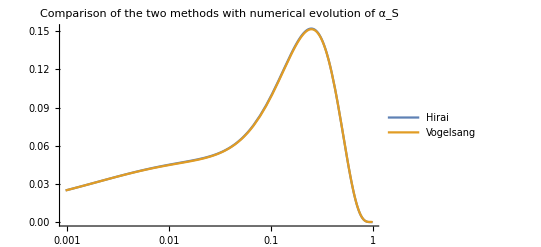

```mathematica
(*Plot[{resInterpolation[x],x*resM[x]},{x,0,1},PlotLegends->{"Hirai","Vogelsang"},ScalingFunctions->{"Log","Linear"},PlotLabel->"Comparison of the two methods with analytical approximation of α_S"]*)
Plot[{resInterpolation[x],x*resM[x]},{x,0,1},PlotLegends->{"Hirai","Vogelsang"},ScalingFunctions->{"Log","Linear"},PlotLabel->"Comparison of the two methods with numerical evolution of α_S"]
```

```mathematica
(*Export["Fig_compare_mathematica_ana.pdf",%]*)
Export["Fig_compare_mathematica_num.pdf",%]
```

Fig_compare_mathematica_num.pdf